```mathematica
Fitness[q_,nu_,qs_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/( BesselI[0,1/nu]),1];
```

```mathematica
a = 0.5;
Q =0.25;
μ = 0.2;
qs = 0.5;
 
g[x_,nu_] :=Q a x/μ NIntegrate[ Fitness[qq, nu, qs]/(μ + a x Fitness[qq,nu,qs]),{qq,0,1}]
```

# Coexistence between generalist and specialits.

#### Optimizing the code

```mathematica
TT= 10^5;
tt1= AbsoluteTiming[
nu = 10;
ff[q_,nu_,qs_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/( BesselI[0,1/nu]),1];
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}];
]
```

{14.3825,Null}

```mathematica
tt2= AbsoluteTiming[
nu = 10;
ff[q_,nu_,qs_]:=Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/( BesselI[0,1/nu]);
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}]
]
```

{13.2175,Null}

```mathematica
tt3= AbsoluteTiming[
nu = 10;
bs =  BesselI[0,1/nu];
ff[q_,nu_,qs_]:=Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/bs;
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}]
]
```

{12.2798,Null}

```mathematica
tt4= AbsoluteTiming[
nu = 10;
bs =  BesselI[0,1/nu];
ff[q_,nu_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/nu]/bs;
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}]
]
```

{11.325,Null}

```mathematica
tt4b= AbsoluteTiming[
nu = 100;
bs =  BesselI[0,1/nu];
ff[q_,nu_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/nu]/bs;
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}]
]
```

{10.7928,Null}

```mathematica
tt5= AbsoluteTiming[
nu = 10;
bs =  Log@BesselI[0,1/nu];
ff[q_,nu_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/nu- bs];
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}]
]
```

{11.2982,Null}

```mathematica
tt6= AbsoluteTiming[
nu = 10;
bs =  Log@BesselI[0,1/nu];
ff[q_,nu_,qs_]:=If[nu == Infinity,1,Exp[ Cos[2 Pi (q-  qs)]/nu]/bs];
 
Do[
aa= Table[ff[q,nu,0.5],{q,0,1,0.1}];
,{times, TT}]
]
```

{11.858,Null}

Without competition

```mathematica
meanQ = 2;
μ = 0.2; 

NQ = 20; (*defines the discretization*)
dQ = 1/NQ;

a= 0.5; (*colonization rate parameter *)
qs = 0.5; (* optimal resource type *)
ν = 0.125; (* niche widht *)

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

fQ = Table[ff[qq,ν,qs],{qq,dQ,1,dQ}];

initp = 0.75;
pO =meanQ/μ ConstantArray[initp,NQ];
TpO = Total[pO]dQ; (* this is total propagule production *) 
allpO= {};

dt = 1.;t=0;
MAXT =100;MAXDT = 2^(-14); MAXDIFF = 10^(-7);diff =10;
While[ t< MAXT && dt> MAXDT && diff >  MAXDIFF,
t+= dt;
Label["here"];
newpO = pO + dt (a  fQ TpO  (meanQ/μ - pO) - μ pO); 

If[Max[newpO]> meanQ/ν, 
dt /= 2; Goto["here"];
 ];

diff = Abs[Total[newpO - pO]];
pO = newpO;
TpO = Total[pO]dQ;
AppendTo[allpO,{t,pO}];
];
cond ={t, dt,diff}
```

{80.5938,0.03125,9.99435×10^-8}

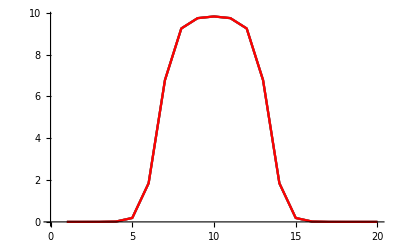

```mathematica
(* MAKING SURE THAT IT CONVERGES: 
newocc is obtained by calculating analytical formula from numerical equilibrium*)
occ= allpO[[-1, 2]];
Istar= Total[occ ] dQ;
newocc = meanQ a Istar fQ/(μ (μ + a Istar fQ));
Istar2= Total[newocc ] dQ;
newocc2 = meanQ a Istar2 fQ/(μ (μ + a Istar2 fQ));

ListLinePlot[{occ,newocc, newocc2},PlotStyle->{Black, Gray,Red}]
```

With competition 2 specialists, z = 0

## Expolartion: Computing overlap

```mathematica
a= 0.5; (*colonization rate parameter *)
qs = 0.5; (* optimal resource type *)
ν = 0.125; (* niche widht *)
```

#### As a function of qS

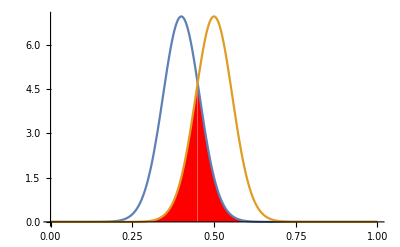

```mathematica
bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs; 

qS1 = 0.40;qS2 = qS1 + 0.1;ν = 0.125;
example1 = Plot[{ff[q,ν, qS1],ff[q,ν, qS2],Min[ff[q,ν, qS1],ff[q,ν, qS2]]},{q,0,1},Filling->{3->{0, Red}},PlotStyle->{Automatic,Automatic,None},PlotRange-> All]
```

```mathematica
qS1 =0.;
ν = 0.125;
bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;
data1= {};
Quiet[
Do[

ovff[q_]:= Min[ff[q,ν, qS1],ff[q,ν, qS1+ dqS]];
ov = NIntegrate[ovff[q],{q,0,1}];
AppendTo[data1,{dqS,ov}];
,{dqS, 0.0,1,0.05}]
];
```

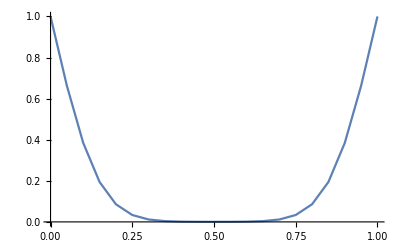

```mathematica
d1 =ListLinePlot[data1]
```

#### As a function of nu

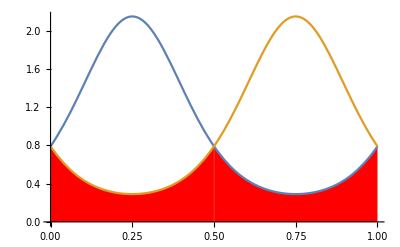

```mathematica
qS1 = 0.25;qS2 = 0.75;ν =1.;

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs; 

example1 = Plot[{ff[q,ν, qS1],ff[q,ν, qS2],Min[ff[q,ν, qS1],ff[q,ν, qS2]]},{q,0,1},Filling->{3->{0, Red}},PlotStyle->{Automatic,Automatic,None},PlotRange->{All,{0,All}}]
```

```mathematica
qS1 =0.25;
qS2 =0.75;
data= {};
Quiet[
Do[

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

ovff[q_]:= Min[ff[q,ν, qS1],ff[q,ν, qS2]];
ov = NIntegrate[ovff[q],{q,0,1}];
AppendTo[data,{ν,ov}];
,{ν, PowerRange[0.1,1000,1.2]}]
];
```

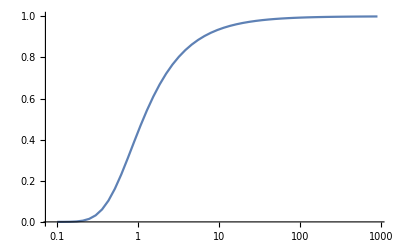

```mathematica
d2 =ListLogLinearPlot[data,Joined->True]
```

## 2 specialists, z = 0, checking coexistence

```mathematica
(*First find the equilibrium for the first species*)
meanQ = 2;
μ = 0.2; 

NQ = 100; (*defines the discretization*)
dQ = 1/NQ;

a= 0.5; (*colonization rate parameter *)
qs = 0.5; (* optimal resource type *)
ν = 10; (* niche widht *)

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

fQ = Table[ff[qq,ν,qs],{qq,dQ,1,dQ}];

initp = 0.75;
pO =meanQ/μ ConstantArray[initp,NQ];
TpO = Total[pO]dQ; (* this is total propagule production *) 
allpO= {};

dt = 1.;t=0;
MAXT =100;MAXDT = 2^(-14); MAXDIFF = 10^(-7);diff =10;
While[ t< MAXT && dt> MAXDT && diff >  MAXDIFF,
t+= dt;
Label["here"];
newpO = pO + dt (a  fQ TpO  (meanQ/μ - pO) - μ pO); 

If[Max[newpO]> meanQ/ν, 
dt /= 2; Goto["here"];
 ];

diff = Abs[Total[newpO - pO]];
pO = newpO;
TpO = Total[pO]dQ;
AppendTo[allpO,{t,pO}];
];
cond ={t, dt,diff};
Which[t> MAXT, Print["time short"], dt ≤  MAXDT,Print["unstable"],diff< MAXDIFF,Print["converged"]];

occR = pO dQ;
```

$Aborted

unstable

```mathematica
(*Compute invasion criteria from  equation 5 Establisment: appendix*)
qsI = qs+0.25 ; (*define the shift in optimal type here*)

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

fQI = Table[ff[qq,ν,qsI],{qq,dQ,1,dQ}];

term1 = Total[fQI occR dQ] ;
term2 = Q/μ - μ/a;
{term1, term2}
```

{0.0115526,0.85}

It looks like by varying the amount of overlap, coexistence between two specialists is always possible

## Solving ODE: 2 specialists, z = 0

```mathematica
meanQ = 2;
μ = 0.2; 

NQ = 40; (*defines the discretization*)
dQ = 1/NQ;

a= 0.5; (*colonization rate parameter *)
qs1 = 0.35; (* optimal resource type *)
qs2 = 0.65; (* optimal resource type *)

ν =0.45; (* niche widht *)

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

fQ1 = Table[ff[qq,ν,qs1],{qq,dQ,1,dQ}];
fQ2 = Table[ff[qq,ν,qs2],{qq,dQ,1,dQ}];

initp = 0.2;
pO1 =meanQ/μ ConstantArray[initp,NQ];
pO2 =meanQ/μ ConstantArray[initp,NQ];
TpO1 = Total[pO1]dQ; (* this is total propagule production *) 
TpO2 = Total[pO2]dQ; (* this is total propagule production *) 
allpO1= {};
allpO2= {};

dt = 1.;t=0;
MAXT =100;MAXDT = 2.^(-20); MAXDIFF = 10^(-9);diff =10;
While[ t< MAXT && dt> MAXDT && diff >  MAXDIFF,
t+= dt;
Label["here"];

newpO1 = pO1 + dt (a  fQ1 TpO1  (meanQ/μ - pO1 - pO2) - μ pO1); 
newpO2 = pO2 + dt (a  fQ2 TpO2  (meanQ/μ - pO1 - pO2) - μ pO2); 

If[Max[newpO1]> meanQ/ν || Max[newpO2]> meanQ/ν Max[newpO1 + newpO2]> meanQ/ν  , 
dt /= 2; Goto["here"];
 ];

diff = Abs[Total[newpO1 - pO1]]+ Abs[Total[newpO2 - pO2]];
pO1 = newpO1;
TpO1 = Total[pO1]dQ;
pO2 = newpO2;
TpO2 = Total[pO2]dQ;
AppendTo[allpO1,{t,pO1}];
AppendTo[allpO2,{t,pO2}];
Which[t> MAXT, Print["time short"], dt ≤  MAXDT,Print["unstable"],diff< MAXDIFF,Print["converged"]];
];
cond ={t, dt,diff};
```

unstable

```mathematica
dt
```

9.53674×10^-7

```mathematica
MAXDT
```

9.53674×10^-7

```mathematica
allpO1
```

{{1.,{1.90059,1.90154,1.90427,1.9121,1.93435,1.99498,2.14968,2.50921,24,1.90002,1.90002,1.90002,1.90002,1.90003,1.90006,1.90011,1.90024}},789,{100.,1}}
 |  |  |  |

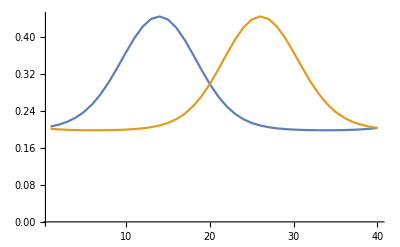

```mathematica
occ1= allpO1[[-1,2]]/(meanQ/μ);
occ2= allpO2[[-1,2]]/(meanQ/μ);
ListLinePlot[{occ1,occ2},PlotRange->All]
```

## Linear fitness function to avoid numerical solution

Defining the new fitness function

The fitness should be linear, as previously, it will be defined by the optimal qS, the lower bound qL and upper bound qU.
The maximum value at qS should be 1/(qU - qS), the fitness f should thus verify, f(qS) = 1/(qU -qS), f(qL) = f(qU) = 0

```mathematica
(*Defining fitness*)
f[q_, qS_,nu_]:=  Module[{qL = qS - nu/2 ,qU  = qS +nu/2,result},
result =Which[
qL≤ q < qS,4./(nu)^2(q - qL), 
qS≤ q < qU,4./( nu)^2(qU- q ),
q< qL || q≥ qU,0.   
];
result];
```

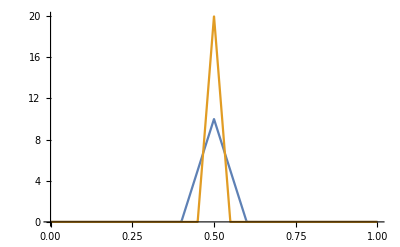

```mathematica
nu =0.2; qS = 0.5;
Plot[{f[q,qS, nu],f[q,qS, nu/2]},{q,0,1},PlotRange-> {{0,1},{0,All}}]
```

Without competition

```mathematica
meanQ = 2;
μ = 0.2; 

NQ = 20; (*defines the discretization*)
dQ = 1/NQ;

a= 0.5; (*colonization rate parameter *)
qs = 0.5; (* optimal resource type *)
ν = 0.3; (* niche widht *)

ff[q_,ν_,qs_]:=f[q, qs, ν];

fQ = Table[ff[qq,ν,qs],{qq,dQ,1,dQ}];

initp = 0.75;
pO =meanQ/μ ConstantArray[initp,NQ];
TpO = Total[pO]dQ; (* this is total propagule production *) 
allpO= {};

dt = 1.;t=0;
MAXT =100;MAXDT = 2^(-14); MAXDIFF = 10^(-7);diff =10;
While[ t< MAXT && dt> MAXDT && diff >  MAXDIFF,
t+= dt;
Label["here"];
newpO = pO + dt (a  fQ TpO  (meanQ/μ - pO) - μ pO); 

If[Max[newpO]> meanQ/ν, 
dt /= 2; Goto["here"];
 ];

diff = Abs[Total[newpO - pO]];
pO = newpO;
TpO = Total[pO]dQ;
AppendTo[allpO,{t,pO}];
];
cond ={t, dt,diff}
```

$Aborted

{1.,4.70847233866529×10^-152044,10}

```mathematica
fQ
```

```mathematica
allpO
```

{}

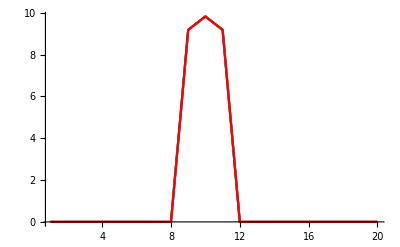

```mathematica
(* MAKING SURE THAT IT CONVERGES: 
newocc is obtained by calculating analytical formula from numerical equilibrium*)
occ= allpO[[-1, 2]];
Istar= Total[occ ] dQ;
newocc = meanQ a Istar fQ/(μ (μ + a Istar fQ));
Istar2= Total[newocc ] dQ;
newocc2 = meanQ a Istar2 fQ/(μ (μ + a Istar2 fQ));

ListLinePlot[{occ,newocc, newocc2},PlotStyle->{Black, Gray,Red},PlotRange->All]
```

## Using NDSolve in Mathematica for the von Mises fitness

```mathematica
MeanField[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+ρE[q][t]* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{systemE,systemO,initialE,initialO}];

variableE=Table[ρE[q],{q,QQ}];
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{variableE,variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
(*TRYING TO MAKE THE CODE FASTER BY REMOVING RESOURCE DYNAMCS*)MeanField2[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

(*initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];*)
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
(*fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];*)

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+(B/μ - Sum[ρ[ssp,q][t],{ssp,NSP}])* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


(*systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];*)
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{(*systemE,*)systemO,(*initialE,*)initialO}];

(*variableE=Table[ρE[q],{q,QQ}];*)
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{(*variableE,*)variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
middata= enddata= {};

qS1 = 0.25;ν =0.125; a =0.5;
com1= {qS1,ν,a };
OTHER ={B = 2,μ = 0.1,NSTEP=200,TMAX = 2000};
time1= AbsoluteTiming[
Do[
com2 = {qS1 + shift,ν, a};
COM = {com1,com2};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,shift];
PrependTo[data2,shift];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{shift,Subdivide[0,0.5,50]}];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\2overlap_qS_midTMAX_NSTEP_200.csv",middata];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\2overlap_qS_endTMAX_NSTEP_200.csv",enddata];
]; (*This takes 64 sec*)
```

```mathematica
time1
```

{64.4724,Null}

```mathematica
data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\2overlap_qS_midTMAX_NSTEP_200.csv"];
data1= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\2overlap_qS_endTMAX_NSTEP_200.csv"];
```

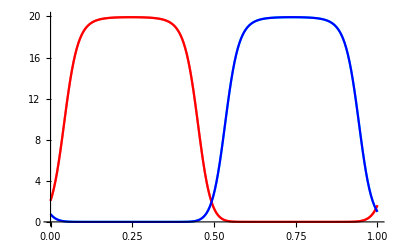

```mathematica
dd = data0[[50]];
sp1 = Transpose[{Subdivide[0.,1,199],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,199],dd[[3]]}];

ee = data1[[50]];
sp1f = Transpose[{Subdivide[0.,1,199],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,199],ee[[3]]}];
ListLinePlot[{sp1,sp2,sp1f,sp2f},PlotStyle->{Pink,Cyan,Red,Blue},PlotRange->{All,{0,B/μ}}]
```

## Change in prevalence as a function of overlap

### Change distance between optimal resource type: ν = 0.125,

```mathematica
middata= enddata= {};

qS1 = 0.25;ν =0.125; a =0.5;
com1= {qS1,ν,a };
OTHER ={B = 2,μ = 0.1,NSTEP=200,TMAX = 2000};
time1= AbsoluteTiming[
Do[
com2 = {qS1 + shift,ν, a};
COM = {com1,com2};
data = MeanField[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,shift];
PrependTo[data2,shift];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{shift,Subdivide[0,0.5,50]}];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_qS_midTMAX_NSTEP_200.csv",middata];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_qS_endTMAX_NSTEP_200.csv",enddata];
];  (*It takes about 86 seconds *)
```

```mathematica
time1
```

{86.7804,Null}

```mathematica
data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_qS_midTMAX_NSTEP_200.csv"];
data1= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_qS_endTMAX_NSTEP_200.csv"];
```

```mathematica
dd = data0[[50]];
sp1 = Transpose[{Subdivide[0.,1,199],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,199],dd[[3]]}];

ee = data1[[50]];
sp1f = Transpose[{Subdivide[0.,1,199],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,199],ee[[3]]}];
ListLinePlot[{sp1,sp2,sp1f,sp2f},PlotStyle->{Pink,Cyan,Red,Blue},PlotRange->{All,{0,B/μ}}]
```

-Graphics-

### Change distance niche width: qS1 = 0.25, qS2 = 0.75

```mathematica
(*Looking at one species*)

middata= enddata= {};

qS1 = 0.25; qS2 =0.75;
a =0.5;
OTHER ={B = 2,μ = 0.1,NSTEP=200,TMAX = 2000};
time2= AbsoluteTiming[
Do[
com1= {qS1 ,ν,a };
com2 = {qS2,ν, a};
COM = {com1(*,com2*)};
data = MeanField[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,PowerRange[0.1,100,1.15]}];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\nu_midTMAX_NSTEP_200.csv",middata];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\nu_endTMAX_NSTEP_200.csv",enddata];
];
(*It just took 33 seconds*)
```

```mathematica
middata= enddata= {};

qS1 = 0.25; qS2 =0.75;
a =0.5;
OTHER ={B = 2,μ = 0.1,NSTEP=200,TMAX = 2000};
time2= AbsoluteTiming[
Do[
com1= {qS1 ,ν,a };
com2 = {qS2,ν, a};
COM = {com1,com2};
data = MeanField[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,PowerRange[0.1,100,1.15]}];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_nu_midTMAX_NSTEP_200.csv",middata];
Export["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_nu_endTMAX_NSTEP_200.csv",enddata];
];
(*It just took 75 seconds*)
```

```mathematica
time2
```

{75.9576,Null}

### Plot for the role of overlap

```mathematica
OTHER ={B = 2,μ = 0.1,NSTEP=200,TMAX = 2000};
```

```mathematica
(* Computing overlap which niche shifts *)

ν = 0.125;
bs =  N@BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;
qS1 = 0.25; ν = 0.125;
ov1= {};
Do[
ovff[q_]:= Min[ff[q,ν, qS1],ff[q,ν, qS1+ shift]];
ov = Quiet[NIntegrate[ovff[q],{q,0,1}]];

AppendTo[ov1,{shift,ov}];
,{shift,Subdivide[0,0.5,50]}];
```

```mathematica
(*Plotting prevalence as a function of overlap*)data= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_qS_endTMAX_NSTEP_200.csv"];
 d1={};
Do[
sp1 = Total[data[[i,2]]]/NSTEP;
(*sp2 = Total[data[[i,3]]]/200;*)
AppendTo[d1,{ov1[[i,1]],ov1[[i,2]],sp1}];

,{i,Length[data]}];
```

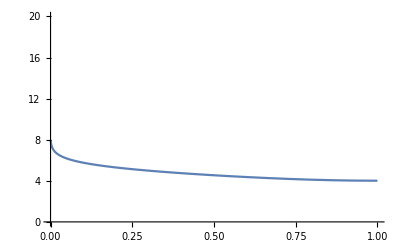

```mathematica
ListLinePlot[d1[[All,{2,3}]],PlotRange->{All,{0,B/μ}}]
```

```mathematica
(*Plotting prevalence as a function of overlap*)data= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_qS_endTMAX_NSTEP_200.csv"];
normsp1 = Total[data[[-1,2]]]/NSTEP;
 d1={};
Do[
sp1 = Total[data[[i,2]]]/NSTEP;
(*sp2 = Total[data[[i,3]]]/200;*)
AppendTo[d1,{ov1[[i,1]],ov1[[i,2]],sp1/normsp1}];

,{i,Length[data]}];
```

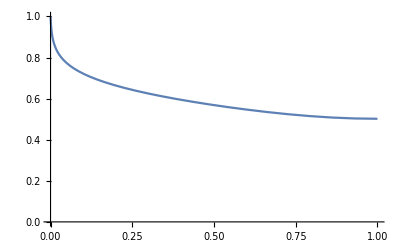

```mathematica
ListLinePlot[d1[[All,{2,3}]],PlotRange->{All,{0,1}}]
```

```mathematica
(* Computing overlap when niche widens *)
qS1 = 0.25; qS2= 0.75;
ov2= {};
Do[
bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

ovff[q_]:= Min[ff[q,ν, qS1],ff[q,ν, qS2]];
ov = Quiet[NIntegrate[ovff[q],{q,0,1}]];
AppendTo[ov2,{ν,ov}];
,{ν,PowerRange[0.1,100,1.15]}];
```

```mathematica
(* Computing occupancy when alone *)

data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\nu_endTMAX_NSTEP_200.csv"];

d2={};
Do[
sp0 = Total[data0[[i,2]]]/NSTEP;
AppendTo[d2,{ov2[[i,1]],sp0}];

,{i,Length[data]}];
```

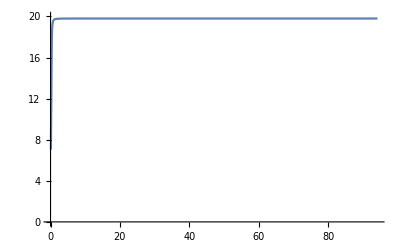

```mathematica
ListLinePlot[d2,PlotRange->{All,{0,B/μ}}]
```

```mathematica
(*Plotting prevalence as a function of overlap, no normalization*)data= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_nu_endTMAX_NSTEP_200.csv"];


d3={};
Do[
sp1 = Total[data[[i,2]]]/NSTEP;

AppendTo[d3,{ov2[[i,1]],ov2[[i,2]],sp1}];

,{i,Length[data]}];
```

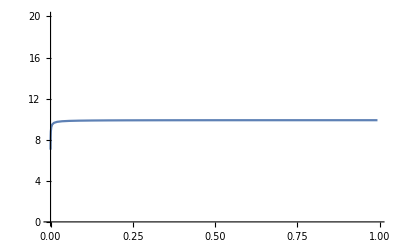

```mathematica
ListLinePlot[d3[[All,{2,3}]],PlotRange->{All,{0,B/μ}}]
```

```mathematica
(*Plotting prevalence as a function of overlap, with normalization*)data= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_nu_endTMAX_NSTEP_200.csv"];

data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\nu_endTMAX_NSTEP_200.csv"];


d3={};
ov3= ov2;
Do[
sp1 = Total[data[[i,2]]]/NSTEP;
sp0 = Total[data0[[i,2]]]/NSTEP;

spf = sp1/sp0 B/μ;
AppendTo[d3,{ov3[[i,1]],ov3[[i,2]],spf}];

,{i,Length[data]}];
```

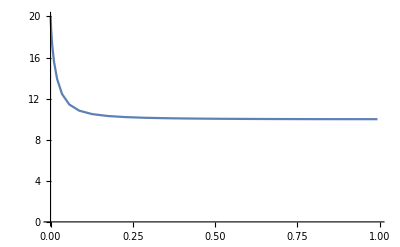

```mathematica
ListLinePlot[d3[[All,{2,3}]],PlotRange->{All,{0,B/μ}}]
```

```mathematica
(*Plotting prevalence as a function of overlap, with normalization*)data= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\overlap_nu_endTMAX_NSTEP_200.csv"];

data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\5_coexistence\\sim1\\nu_endTMAX_NSTEP_200.csv"];


d3={};
ov3= ov2;
Do[
sp1 = Total[data[[i,2]]]/NSTEP;
sp0 = Total[data0[[i,2]]]/NSTEP;

spf = sp1/sp0 ;
AppendTo[d3,{ov3[[i,1]],ov3[[i,2]],spf}];

,{i,Length[data]}];
```

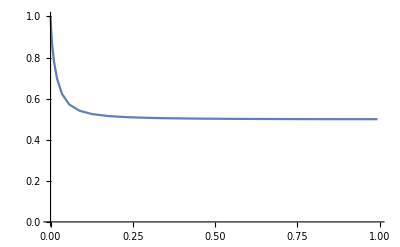

```mathematica
ListLinePlot[d3[[All,{2,3}]],PlotRange->{All,{0,1}}]
```